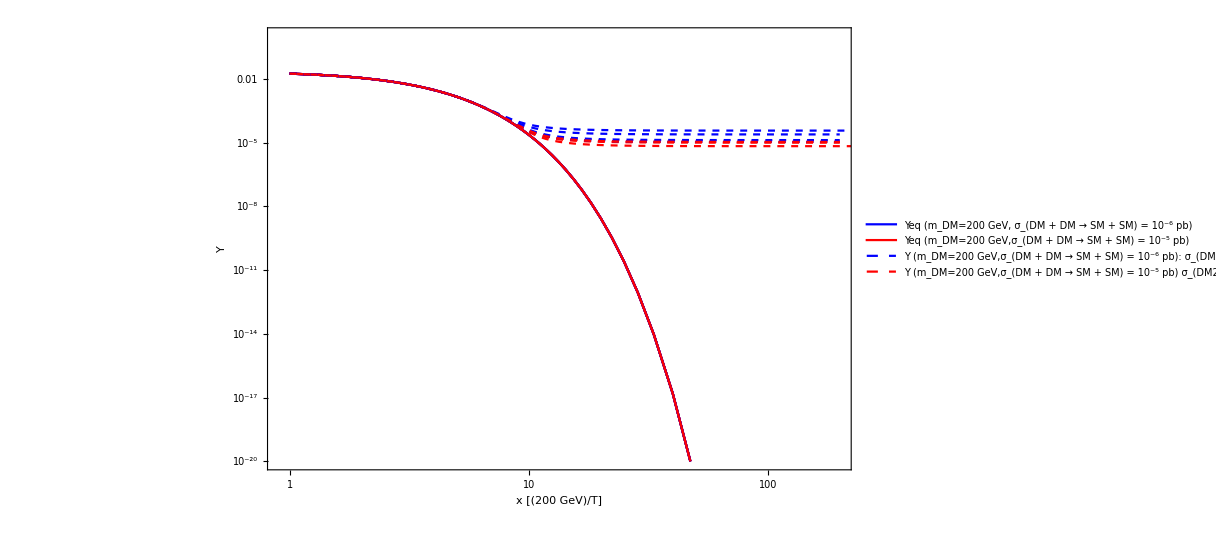

```mathematica
fileNames = {"C:\\Users\\AlexandrePoulin\\Documents\\relic\\twoDM\\out1_a6.txt",
			"C:\\Users\\AlexandrePoulin\\Documents\\relic\\twoDM\\out2_a6.txt",
			"C:\\Users\\AlexandrePoulin\\Documents\\relic\\twoDM\\out3_a6.txt",
			"C:\\Users\\AlexandrePoulin\\Documents\\relic\\twoDM\\out4_a6.txt"};
files = Import[#,"Data"]&/@fileNames;

massScale= 200.0;
dmSpecies = 2;

plotDataeq = {};
plotData = {};

numFilesToUse=4;

For[i=1, i ≤ numFilesToUse,i++,
For[j=1, j≤ dmSpecies,j++,
AppendTo[plotDataeq,Table[{massScale/files[[i]][[a]][[1]],files[[i]][[a]][[2*j]]},{a,Length[files[[i]]]}]];
AppendTo[plotData,Table[{massScale/files[[i]][[a]][[1]],files[[i]][[a]][[2*j+1]]},{a,Length[files[[i]]]}]];
]
]


plot1=ListLogLogPlot[plotDataeq,PlotRange->{{0.9,200},{10^(-20),1}},Joined->True,PlotStyle->{Blue,Red,Blue,Red,Blue,Red, Blue,Red,Blue,Red},PlotLegends->{"Yeq (m_DM=200 GeV, σ_(DM + DM → SM + SM) = 10^-6 pb)","Yeq (m_DM=200 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)"}];
plot2=ListLogLogPlot[plotData,PlotRange->{{0.9,200},{10^(-20),1}},Joined->True,PlotStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Blue},{Dashed,Red},{Dashed,Blue},{Dashed,Red},{Dashed,Blue},{Dashed,Red},{Dashed,Blue},{Dashed,Red}},PlotLegends->{"Y (m_DM=200 GeV,σ_(DM + DM → SM + SM) = 10^-6 pb): \nσ_(DM2 + DM2 → DM1 + DM1) = 0 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-6 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-5 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-4 pb","Y (m_DM=200 GeV,σ_(DM + DM → SM + SM) = 10^-5 pb)\nσ_(DM2 + DM2 → DM1 + DM1) = 0 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-6 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-6 pb, \nσ_(DM2 + DM2 → DM1 + DM1) = 10^-4 pb"}];
Show[{plot1,plot2},BaseStyle->{FontSize->40},Frame-> True,FrameLabel->{"x [(200 GeV)/T]","Y"},FrameStyle->Thick,FrameTicksStyle->Thick,ImageSize->{900,600}]
```